## Definiciones

```mathematica
Clear[sz,sx,sy,id,Jz,Jx,Jy,JM,Jm,H2,H3,eisys];
sz={{1,0},{0,-1}};
sx={{0,1},{1,0}};
sy=(I){{0,-1},{1,0}};
id=IdentityMatrix[2];
Jz=(1/2)(KroneckerProduct[sz,id]+KroneckerProduct[id,sz]);
Jx=(1/2)(KroneckerProduct[sx,id]+KroneckerProduct[id,sx]);
Jy=(1/2)(KroneckerProduct[sy,id]+KroneckerProduct[id,sy]);
JM=(1/2)(Jx+(I)(Jy));
Jm=(1/2)(Jx-(I)(Jy));
H2[a_,b_,c_]:=(a)(Jz)+(b/(2J))(Jx.Jx)+(c/(2J))(Jy.Jy);

(*Diagonalizacion*)
eisys[a_,b_,c_]:=eisys[a,b,c]=Module[{eigenvec,eigenval},

{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[H2[a,b,c]]]]];

{eigenval,eigenvec}
];
```

## Energias

{{0.,2.5},{0.314159,2.11803},{0.628319,1.11803},{0.942478,-0.118034},{1.25664,-1.11803},{1.5708,-1.5},{1.88496,-1.11803},{2.19911,-0.118034},{2.51327,1.11803},{2.82743,2.11803},{3.14159,2.5},{3.45575,2.11803},{3.76991,1.11803},{4.08407,-0.118034},{4.39823,-1.11803},{4.71239,-1.5},{5.02655,-1.11803},{5.34071,-0.118034},{5.65487,1.11803},{5.96903,2.11803},{6.28319,2.5}}

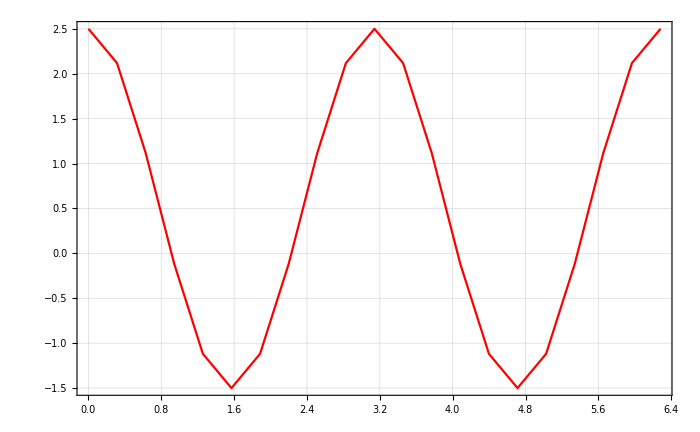

```mathematica
Clear[state,x, analitical,trial0];
J=2;
state[x_]:={-Cos[x],0,0,Sin[x]};
analitical=Table[{i,Conjugate[state[i]].H2[2,2,2].state[i]//Chop}, {i,Range[0,2Pi,0.1Pi]}]
trial0=ListPlot[analitical, Joined->True, PlotStyle->Red, PlotTheme->"Detailed",ImageSize->700]
```

```mathematica
angles=Range[0,2Pi,0.1Pi]
```

{0.,0.314159,0.628319,0.942478,1.25664,1.5708,1.88496,2.19911,2.51327,2.82743,3.14159,3.45575,3.76991,4.08407,4.39823,4.71239,5.02655,5.34071,5.65487,5.96903,6.28319}

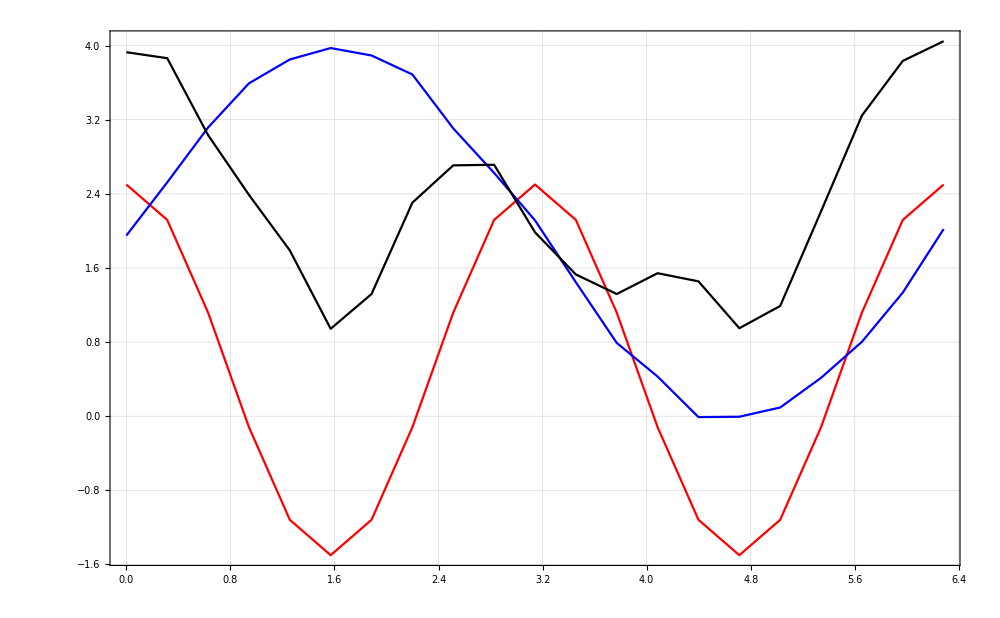

```mathematica
energies={1.94921875,2.5234375,3.115234375,3.591796875,3.849609375,3.97265625,3.892578125,3.6875,3.10546875,2.625,2.11328125,1.4453125,0.791015625,0.427734375,-0.009765625,-0.005859375,0.09375,0.4140625,0.802734375,1.333984375,2.01953125};
energies=ArrayReshape[energies,{Length[angles]}];

energies2={3.927734375,3.86328125,3.033203125,2.388671875,1.7890625,0.943359375,1.318359375,2.3046875,2.70703125,2.712890625,1.984375,1.529296875,1.318359375,1.54296875,1.455078125,0.94921875,1.189453125,2.2109375,3.244140625,3.833984375,4.046875};
energies2=ArrayReshape[energies2,{Length[angles]}];

data={};
Do[
AppendTo[data,{angles[[i]],energies[[i]]}]

,{i,1,Length[angles]}];
trial1 =ListPlot[data,PlotTheme->"Detailed",ImageSize->700,Ticks->Automatic,PlotStyle->Blue, Joined->True];

data2={};
Do[
AppendTo[data2,{angles[[i]],energies2[[i]]}]

,{i,1,Length[angles]}];
trial2 =ListPlot[data2,PlotTheme->"Detailed",ImageSize->700,Ticks->Automatic,PlotStyle->Black,Joined->True];

Show[trial0, trial1,trial2,PlotRange->All,PlotTheme->"Detailed",ImageSize->1000]
```